# Calculus

To do / notes for self:
	- Using graphs to improve intuition
	- Faster function input / chaining

```mathematica
Factor[x^2+2 x+1]
```

(1+x)^2

## General fluency

### Use plots

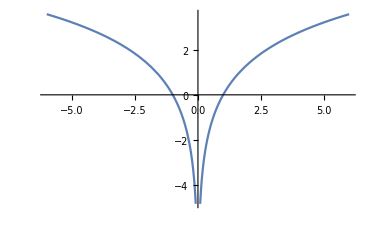

```mathematica
Plot[Log[x^2], {x, -6., 6.}]
```

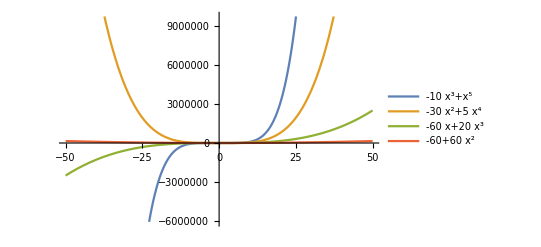

```mathematica
NestList[D[#, x]&, x^5-10 x^3, 3]// Plot[#,{x, -50, 50}, PlotLegends->"Expressions"]&
```

### Use natural language input

WolframAlphaQueryResults

| number of possible hands | approximate probability | approximate chance
5-card hand | 3744 | 0.001441 |  ≈  1 in 694
7-card hand | 3473184 | 0.02596 |  ≈  1 in 39(assuming random selection from a standard 52-card deck)
(the value of a 7-card hand is determined by its best 5-card subset)

WolframAlphaQueryResults

206379406870

### Take advance of the suggestion bar

You can also use it to plot without having to type in the rnage.

```mathematica
D[x*Sin[x] - Sec[x], x]
```

x Cos[x]+Sin[x]-Sec[x] Tan[x]

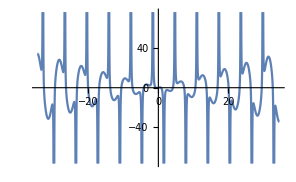

```mathematica
Plot[x Cos[x]+Sin[x]-Sec[x] Tan[x],{x,-34.55751918948772,34.55751918948772}]
```

## Limits

## Derivatives

```mathematica
D[(3 - 14x)^2, x]
```

-28 (3-14 x)

```mathematica
D[Log[x^2], x]
```

2/x

## Understanding functions

Let us say we are given the following expression

```mathematica
Clear[f]
f [x_]:= x/((x^2-1)^(1/3));
```

Plot the function and its domain

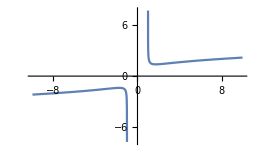

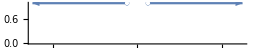

```mathematica
Plot[f[x], {x, -10, 10}]
FunctionDomain[f[x],x] //NumberLinePlot[#, {x, -10, 10}]&
```

```mathematica
f'[x] //FullSimplify
f''[x] // FullSimplify
```

(-3+x^2)/(3 (-1+x^2)^(4/3))

-(2 x (-9+x^2))/(9 (-1+x^2)^(7/3))

Critical points are points where the derivative is zero or does not exist.

```mathematica
Solve[(-3+x^2)/(3 (-1+x^2)^(4/3))==0, x]
```

{{x→-√3},{x→√3}}

```mathematica
(-3+x^2)/(3 (-1+x^2)^(4/3)) // FunctionDomain[#, x]&
```

x<-1||x>1

## Integrals

## Other

Solving functions over a range

```mathematica
f[x_]:=Sin[x]/(2+Cos[x])
Solve[f'[x]==0&&-5≤x≤5,x] // AbsoluteTiming
Reduce[{f'[x] == 0, -5 ≤ x ≤ 5}] //AbsoluteTiming
```

{0.0451677,{{x→-(4 π)/3},{x→-(2 π)/3},{x→(2 π)/3},{x→(4 π)/3}}}

{0.0427859,x==-(4 π)/3||x==-(2 π)/3||x==(2 π)/3||x==(4 π)/3}